```mathematica
Eq = Expand[(f.q + 1/2)^2 == (f .f+ f.q + 1/4) + I (f.q + 1/2)]
```

1/4+f.q+(f.q)^2==(1/4+ⅈ/2)+f.f+(1+ⅈ) f.q

```mathematica
Solve[Eq, f.q]
```

{{f.q→1/2 (ⅈ-√((-1+2 ⅈ)+4 f.f))},{f.q→1/2 (ⅈ+√((-1+2 ⅈ)+4 f.f))}}

```mathematica
DC[k_, M_] := 2 Sin[Pi/M]{-Sin[2 Pi k/M], Cos[2 Pi k/M], 0};
```

```mathematica
RandomInitialF0 := f0 = RandomReal[{-1,1},3] +I {RandomReal[{-1,1}],RandomReal[{0,1}],RandomReal[{-1,1}]};
```

```mathematica
ArgMinList[L_List]:=  Position[L,Min @@L];
ArgMaxList[L_List]:=  Position[L,Max @@L];
MyNorm[V_] := Evaluate[Sqrt[Re[V].Re[V] + Im[V].Im[V]]]; 
MySqr[V_] := Evaluate[Re[V].Re[V] + Im[V].Im[V]];
```

```mathematica
XY[ R_, {a_,b_,c_},z_] :=
Inverse[{{ Re[a] , Re[b]}, { Im[a] , Im[b]}}].{Re[R]  - z Im[c], 
Im[R]  + z Re[c]};
```

```mathematica
QSol[f_, σ_]:= Block[{x,y,z},
{x,y} =XY[1/2(I+ σ Sqrt[4 f.f -1 + 2 I]),f ,z];
{x,y,I z}/.Solve[x^2 + y^2- z^2==1,{z}]
]//Quiet;
```

```mathematica
NumericVectors[X_List]:= Select[X,#==Select[#,NumericQ]&]
```

```mathematica
NumericVectors[{{1,2,3},{a,2,4},{I,2,6}}]
```

{{1,2,3},{ⅈ,2,6}}

```mathematica
(#.#)& /@QSol[{1,I, 3},-1]//Simplify
```

{1,1}

```mathematica
RandomChoice[{1}]
```

1

```mathematica
ClearAll[RW];
```

```mathematica
RW[M_,f0_]:= 
Block[{dist,f,flist, O,f1,  q,qq,X,n, norms},
f = f0;
flist = {f}; 
dist = CircularRealMatrixDistribution[3];
For[k =0, k < M,k++,
O = RandomVariate[dist];
f1 =Transpose[O].f ;
X = Join[QSol[f1,-1 ],QSol[f1,1 ]];
qq =NumericVectors[Select[X, Re[#[[3]]]==0&]];
If[Length[qq] >0 ,
(*Echo[Length[qq],"qq after real beta selected :"];*)
qq =NumericVectors[Select[qq,Im[ (f + O.#)].DC[Length[flist], M] >=0&]];
(*Echo[Length[qq],"qq after Im F DC >0 selected :"];*)
If[Length[qq] >0 ,
norms =MyNorm[#]&/@qq;
f += O.qq[[ArgMinList[norms][[1,1]]]];
 AppendTo[flist,f]
];(*If*)
(*Echo[Length[flist],"flist:"];*)
];
];(*While*)
flist
];(*Block*)
```

```mathematica
StatisticalDistributions[M_, L_,K_, WhichTable_]:= 
Block[{stats,l,  datas, names},
datas =
Transpose[
WhichTable[
Block[{f0,  rw},
f0 = RandomInitialF0;
rw = RW[M, f0];
{
Log[MyNorm[rw[[#]]-f0]] & /@ Range[K,Length[rw]],
MyNorm[rw[[#]]-rw[[#-1]]] & /@ Range[K,Length[rw]],
Re[-(Cross[rw[[#]],rw[[#-1]]])^2 ]& /@ Range[K,Length[rw]]
}
],{l,L}]
]; 
names = { "walk","step", κ};
{datas, names}
];
```

```mathematica
{datas, names } = StatisticalDistributions[1000, 10000, 10, ParallelTable];
```

```mathematica
Dimensions[datas]
```

{3,10000}

```mathematica
WalkPlot[stat_, part_, funcs_] :=
Block[{gaps, CDFTail,ld, mlen,tail,model,x},
mlen = Floor[Mean[Length[#] &/@ stat]];
(*Echo[mlen];*)
gaps = #[[;;mlen]]& /@Select[stat,Length[#] >= mlen & ];
(*Echo[Dimensions[gaps]];*)
ld = Mean[#] & /@ Transpose[gaps];
 data =Transpose[{Log [Range[mlen]],ld}];
tail = Floor[part mlen];
model =LinearModelFit[data[[-tail;;]],funcs,ξ];
Print["random walk :"];
Print[Quiet[model["ParameterTable"]]];
Show[ListPlot[data[[-tail;;]], PlotStyle->{Red,Thick}, PlotLegends->{"data"}], Plot[ model["BestFit"], {ξ,Log[mlen-tail], Log[mlen]},PlotStyle->{Blue,Dashed},PlotLegends->{"fit"}],PlotLabel->model["BestFit"]/.ξ->Log[Steps], AxesLabel->{Log[Steps],Log[Dist]},PlotRange->Full]
];
```

random walk :

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.51345 | 0.037324 | -40.5488 | 1.99343×10^-28
ξ | 0.831889 | 0.00713645 | 116.569 | 1.5485×10^-42

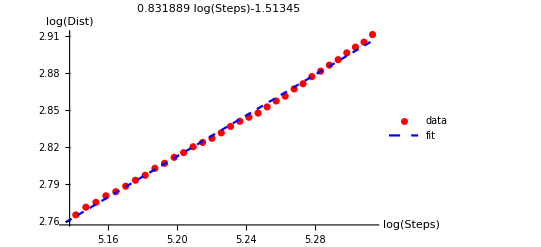

```mathematica
WalkPlot[datas[[1]],1/6, {1,ξ}]
```

```mathematica
1/0.8318890075470246
```

1.20208

```mathematica
StatPlots[stat_, name_,  funcs_, lastN_, stepN_] :=
Block[{ld,srt,var, fitData,weights, mlen,model,ξ, delta, NumAbove},
srt = N[Select[Flatten[stat], #>0&]];
Print[name, " flattened, dimensions:", Dimensions[srt]];
srt = Sort[srt];
Print[name, "sorted :", Mean[srt], "+/-", Sqrt[Variance[srt]]];
ld = Log[srt];
mlen = Length[ld];
Print[" min len before :", mlen];
fitdata =ParallelTable[{ld[[n]],Log[(mlen -n+1)]},{n,mlen-lastN,mlen-stepN}];
model =LinearModelFit[fitdata,funcs,ξ];
Print[Quiet[model["ParameterTable"]/.ξ->Log[name]]];
Show[{ListPlot[fitdata, PlotStyle->{Red,Thick}, PlotLegends->{"data"}], Plot[ model["BestFit"], {ξ,ld[[mlen-lastN]], ld[[mlen-stepN]]},PlotStyle->{Blue,Dashed},PlotLegends->{"fit"}]},
PlotLabel->model["BestFit"]/.ξ->Log[name],
 AxesLabel->{Log[name],Log[NumAbove]},PlotRange->Full]
];
```

step flattened, dimensions:{2039074}

stepsorted :1.13242+/-14.5394

min len before :2039074

| Estimate | Standard Error | t-Statistic | P-Value
1 | 9.73639 | 0.00311242 | 3128.24 | 0.
Log[step] | -1.05541 | 0.000951541 | -1109.16 | 0.

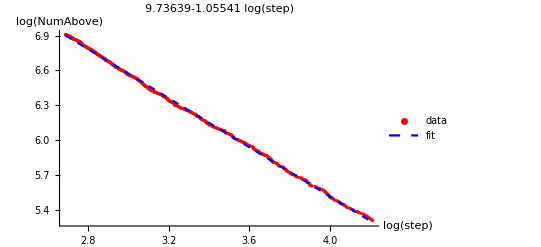

```mathematica
StatPlots[datas[[2]], names[[2]],{1,ξ},1000,200]
```

κ flattened, dimensions:{2759224}

κsorted :31817.2+/-3.52173×10^7

min len before :2759224

| Estimate | Standard Error | t-Statistic | P-Value
1 | 14.1307 | 0.00177546 | 7958.9 | 0.
Log[κ] | -0.661336 | 0.000173123 | -3820.03 | 0.

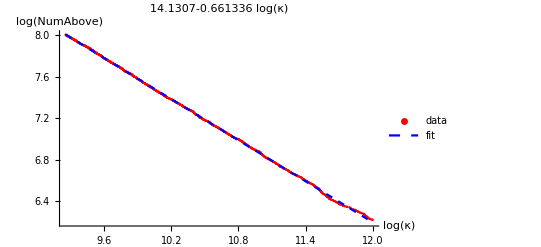

```mathematica
StatPlots[datas[[3]], names[[3]],{1,ξ},3000,500]
```

```mathematica
TD[a_] := Table[{t, 1/(t + a) + RandomReal[{-0.1,0.1}]},{t,1,5,0.1}];
```

```mathematica
nlm =FindFit[TD[-0.5],b t^(-n),{b,n}, t]
```

{b→1.91251,n→1.45403}

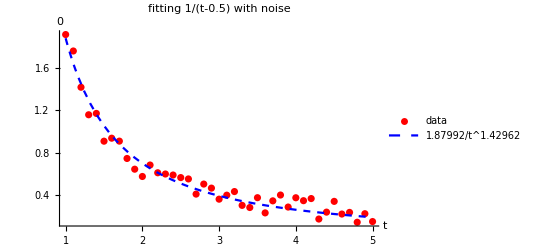

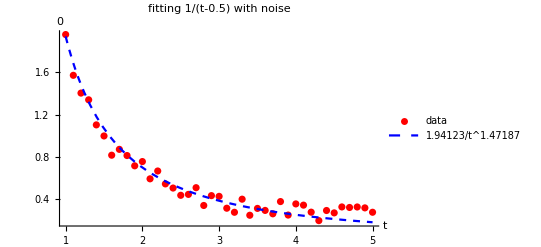

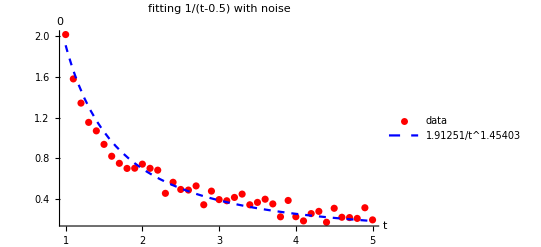

```mathematica
Show[{ListPlot[TD[-0.5], PlotStyle->{Red,Thick}, PlotLegends->{"data"}], Plot[b t^(-n)/.nlm,{t,1,5}, PlotLegends->{b t^(-n)/.nlm},PlotStyle->{Blue,Dashed}]},
PlotLabel->"fitting 1/(t-0.5) with noise",
 AxesLabel->{t,E'[t]},PlotRange->Full]
```